## Setup

#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell"]["Wolfram`TensorNetworks`",
FileNameJoin[{NotebookDirectory[],"..","TensorNetworks"}]]
```

## Playground

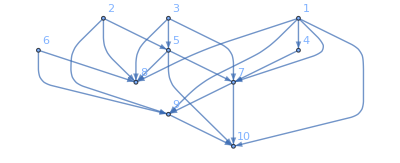

```mathematica
net=GraphTensorNetwork[RandomGraph[{10,20}],Method->"RandomComplex"]
```

```mathematica
ContractTensorNetwork[net]//AbsoluteTiming
```

{0.005886,-71.2022-183.715 ⅈ}

```mathematica
ContractTensorNetwork[net,Method->"Naive"]//AbsoluteTiming
```

{1.80955,-71.2022-183.715 ⅈ}

```mathematica
path=TensorNetworkContractionPath[net,Method->"max"]
```

{{5,7},{6,9},{7,8},{6,7},{2,6},{3,5},{3,4},{2,3},{1,2}}

```mathematica
Activate/@AssociationMap[TensorNetworkContraction[net,path,Method->#]&,$TensorNetworkContractionMethods]
```

<|ArrayDotTranspose→-71.2022-183.715 ⅈ,ArrayDot→-71.2022-183.715 ⅈ,Dot→-71.2022-183.715 ⅈ,TensorContract→-71.2022-183.715 ⅈ,TableSum→-71.2022-183.715 ⅈ|>